## Question 2

```mathematica
Clear["Global`*"]
```

```mathematica
r=26.5; σ = 10; b = 8/3;
```

```mathematica
sol = NDSolve[{x'[t]==σ (-x[t]+y[t]),y'[t]==-x[t] z[t]+r x[t]-y[t],z'[t]==x[t] y[t]- b z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,200},MaxSteps->Infinity]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>],z→InterpolatingFunction[{{0.,200.}},<>]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.%],{t,0,200},PlotPoints->100000,ColorFunction->(ColorData["Rainbow"][#4]&)]
```

-Graphics3D-

```mathematica
xg=Plot[x[t]/. sol,{t,0,50},PlotStyle->{Red}];
yg=Plot[y[t]/. sol,{t,0,50},PlotStyle->{Blue}];
zg=Plot[z[t]/. sol,{t,0,50},PlotStyle->{Green}];
```

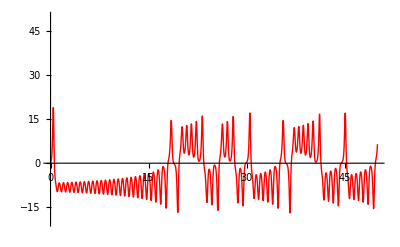

```mathematica
Show[xg,PlotRange->{-20,50}]
```

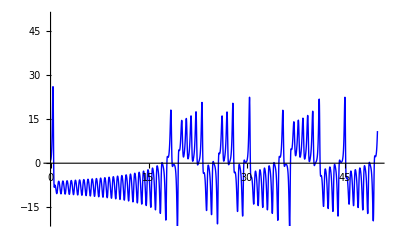

```mathematica
Show[yg,PlotRange->{-20,50}]
```

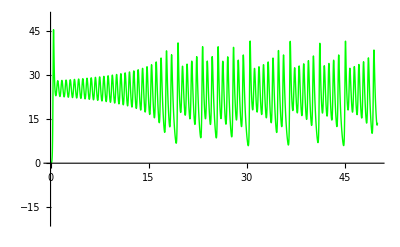

```mathematica
Show[zg,PlotRange->{-20,50}]
```

```mathematica
Looks pretty chaotic
```